## Definitions

```mathematica
(*kinematic equations*)
s[t_,s0_,u0_,g_]:=s0+u0*t+1/2*g*t^2;
(*Bragg mirror pulse*)
vbragg[v_,dv_]:=v-Sign[v]*Abs[dv];
```

```mathematica
(*Derived Parameters*)
λ[vz_]:=h/(mhe*vz);(*de Broigle wavelength along the z axis*)
V[vz_]:=2*λ[vz]*Abs[g0]/vz^2;(*Measure of how valid the semi-classical approximation is*)
φ[vz_,g_,t_,z0_,m_,vr_]:=FullSimplify[UnitSimplify[Integrate[1/2*m*(vr^2+(vz+g*τ)^2)-m*g*(z0+vz*τ+1/2*g*τ^2),{τ,0,t}]]];
```

## Parameters

```mathematica
(*Experimental Parameters*)
vradius=Quantity[60,"mm/s"];
dvbragg=-2*u;
t=Quantity[1,"second"];
```

```mathematica
(*Physical constants*)
mhe= Entity["Element", "Helium"][EntityProperty["Element", "AtomicMass"]]; (*mass of helium*)
e=Entity["Particle", "Electron"][EntityProperty["Particle", "Charge"]];
c=Quantity[None, "SpeedOfLight"];
ϵ=Quantity[None, "ElectricConstant"];
me=Entity["Particle", "Electron"][EntityProperty["Particle", "Mass"]];
h=Quantity[None, "PlanckConstant"];
kb=Quantity[None, "BoltzmannConstant"];
g=Quantity[9.81,"m/s^2"];
```

## Experimental Setup

```mathematica
SetOptions[ParametricPlot, BaseStyle -> {FontFamily -> "Times", FontSize -> 30},
   Frame -> True, ImageSize -> 72*{8, 8*GoldenRatio}, 
  AspectRatio->Automatic, LabelStyle -> Directive[Bold, FontSize -> 30,FontFamily -> "Times",FontColor->Black], 
  GridLines -> Automatic,PlotStyle->{AbsoluteThickness[3.5]}];
```

```mathematica
(*Diagram of our experiment in initial velocity space and paths through real space*)
```

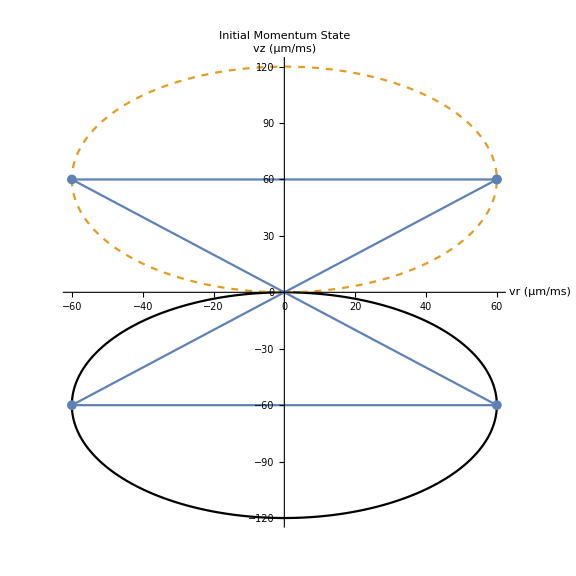

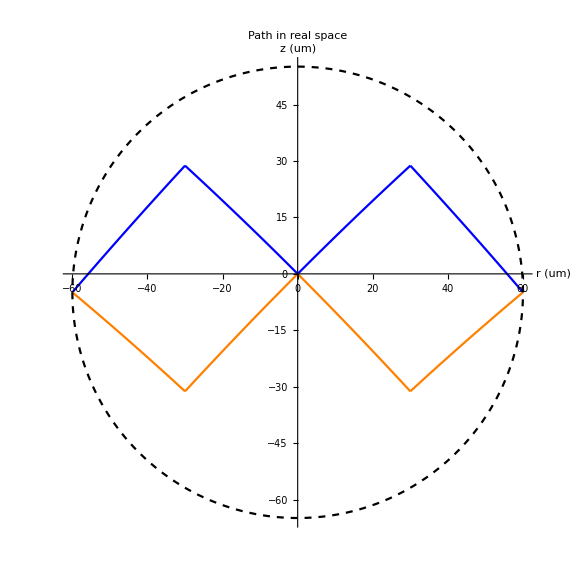

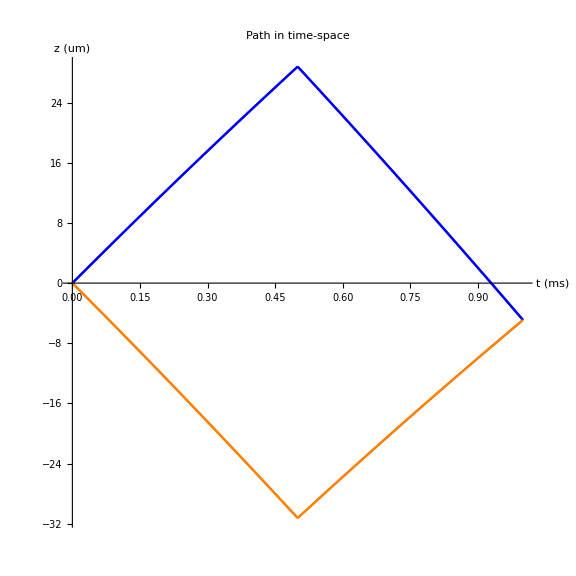

```mathematica
ϕ=0;
g0=-9.81;
u=60;(*in mm/s*)
dv=-2*u;
tf=1;(*in milliseconds*)
vr=u*Cos[ϕ];
vz=u*Sin[ϕ]+u;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
p1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
vr=u*Cos[ϕ+Pi];
vz=u*Sin[ϕ+Pi]+u;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
pc1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
pc1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p5=ParametricPlot[{Cos[θ]*u*tf, (Sin[θ]*u+u)*tf+g0*tf^2/2-u*tf}, {θ, -Pi,Pi},PlotStyle->{Black,Dashed}];
p6=ParametricPlot[{{Cos[θ]*u, (Sin[θ]*u-u)},{Cos[θ]*u, (Sin[θ]*u+u)}}, {θ, -Pi,Pi},PlotStyle->{Black,Dashed}];
p7=ListPlot[{{u*Cos[ϕ],u*Sin[ϕ]+u},{u*Cos[ϕ+Pi],u*Sin[ϕ+Pi]+u},{u*Cos[ϕ],u*Sin[ϕ]-u},{u*Cos[ϕ+Pi],u*Sin[ϕ+Pi]-u},{u*Cos[ϕ],u*Sin[ϕ]+u}},PlotMarkers->{Automatic,10},Joined->True];
Show[p6,p7, ImageSize -> 72*{8, 8},AxesLabel->{"vr (μm/ms)","vz (μm/ms)"},PlotLabel ->"Initial Momentum State"]
Show[p2,p1,pc2,pc1,p5,PlotRange->All,AxesLabel->{"r (um)","z (um)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20},PlotRange -> {{-60, 60}, {-60,60}},AspectRatio->1, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in real space"]
Show[p2t,p1t,pc2t,pc1t,PlotRange->All,AxesLabel->{"t (ms)","z (um)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20},PlotRange -> {{-60, 60}, {-60,60}},AspectRatio->1, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in time-space"]
```

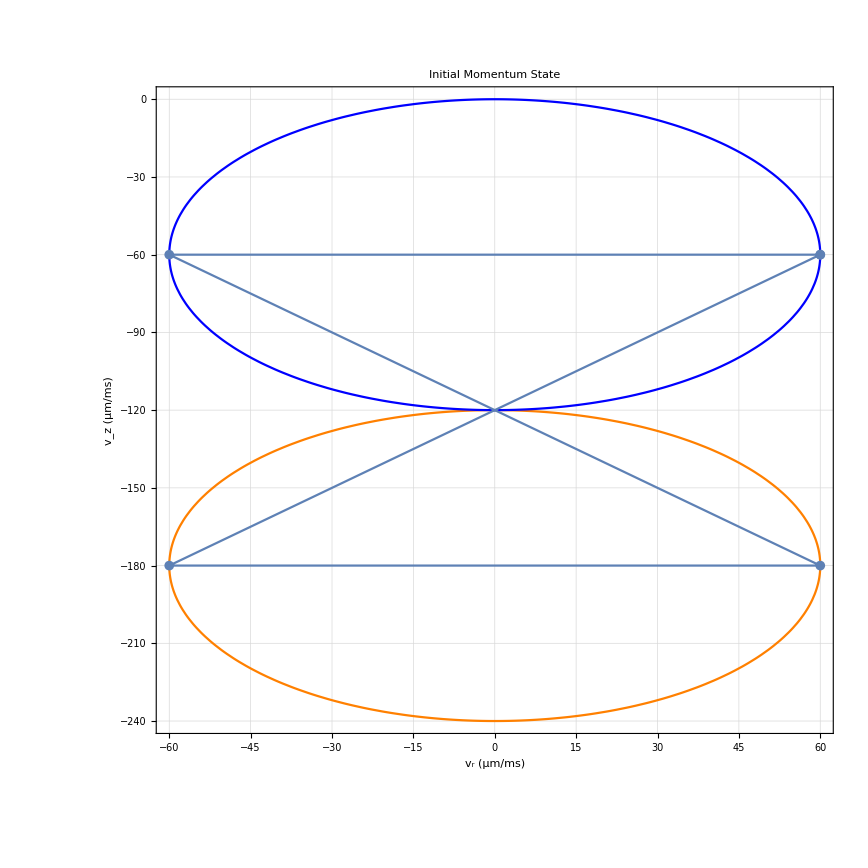

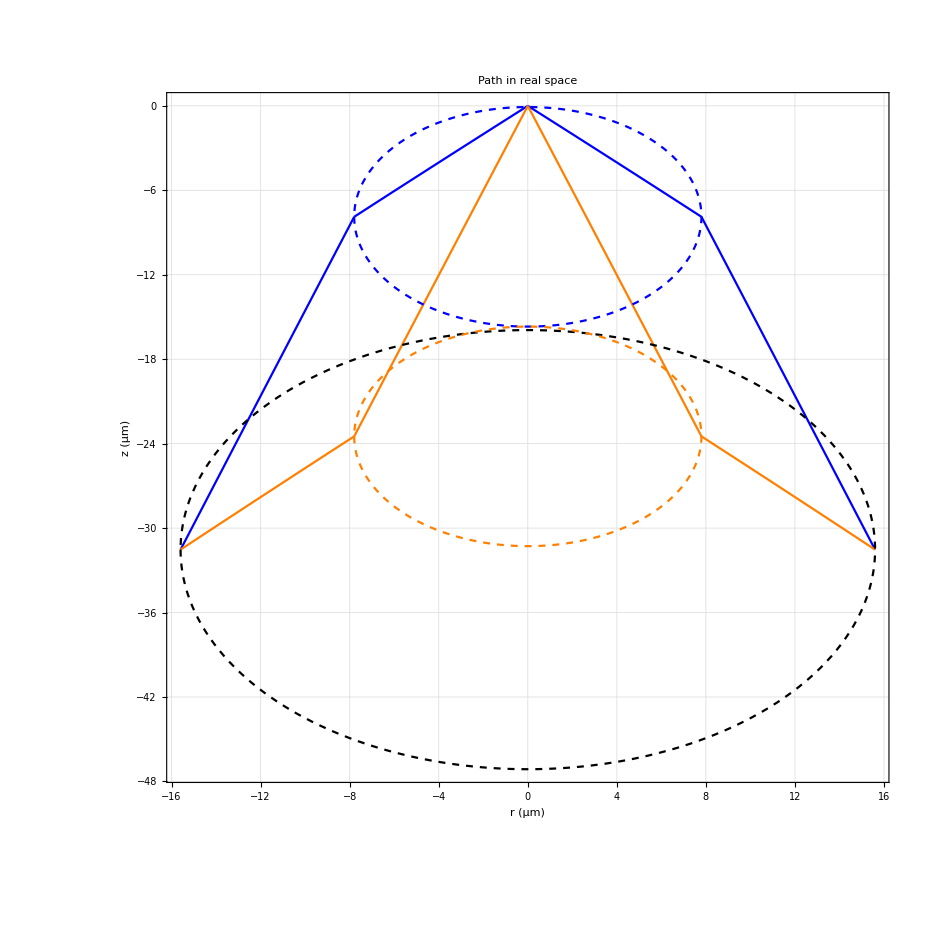

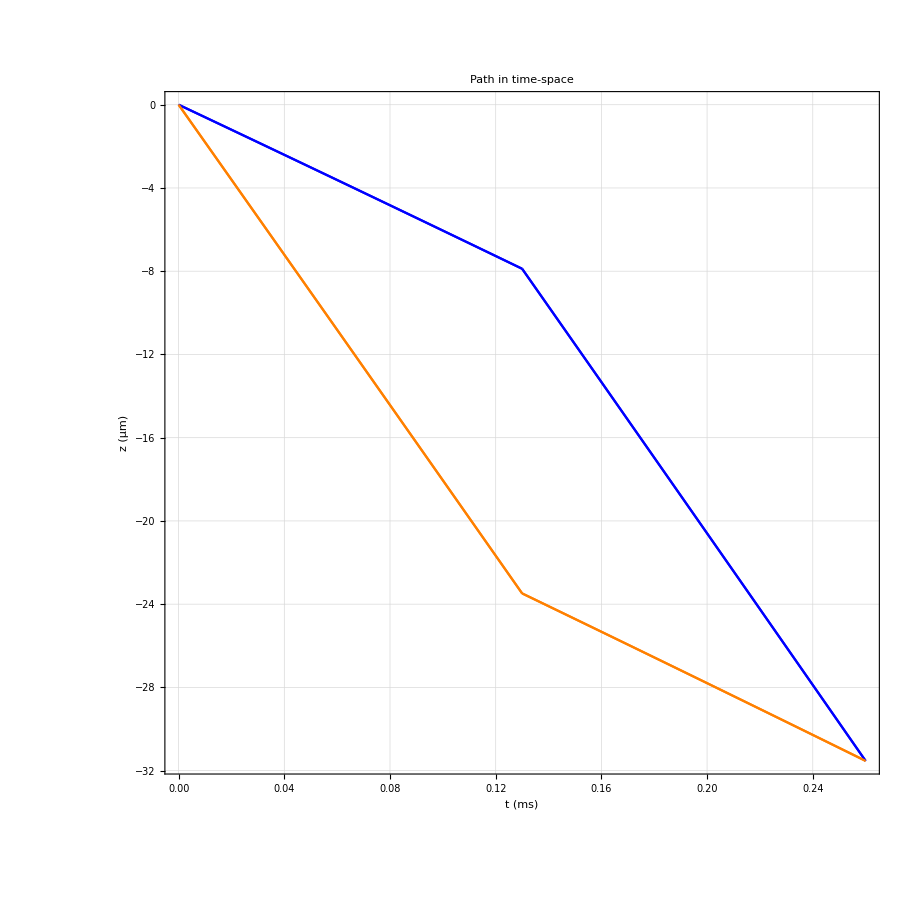

```mathematica
ϕ=0;
g0=-9.81;
u=60;(*in mm/s*)
dv=-2*u;
offset = -2*u;
tf=0.26;(*in milliseconds*)
vr=u*Cos[ϕ];
vz=u*Sin[ϕ]+u+offset;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
(*propogting in the positive direction*)
p1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
vr=u*Cos[ϕ+Pi];
vz=u*Sin[ϕ+Pi]+u+offset;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
th=ParametricPlot[{Cos[θ]*u*tf/2, (Sin[θ]*u-u)*tf/2+1/2*g0*tf^2/4}, {θ, -Pi,Pi},PlotStyle->{Blue,Dashed}];
bh=ParametricPlot[{Cos[θ]*u*tf/2, (Sin[θ]*u-u+offset)*tf/2+1/2*g0*tf^2/4}, {θ, -Pi,Pi},PlotStyle->{Orange,Dashed}];
pc1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
pc1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p5=ParametricPlot[{Cos[θ]*u*tf, Sin[θ]*u*tf+g0*tf^2/2+offset*tf}, {θ, -Pi,Pi},PlotStyle->{Black,Dashed}];
p6=ParametricPlot[{{Cos[θ]*u, (Sin[θ]*u-u)+offset},{Cos[θ]*u, (Sin[θ]*u+u)+offset}}, {θ, -Pi,Pi},PlotStyle->{Orange,Blue}];
p7=ListPlot[{{u*Cos[ϕ],u*Sin[ϕ]+u+offset},{u*Cos[ϕ+Pi],u*Sin[ϕ+Pi]+u+offset},{u*Cos[ϕ],u*Sin[ϕ]-u+offset},{u*Cos[ϕ+Pi],u*Sin[ϕ+Pi]-u+offset},{u*Cos[ϕ],u*Sin[ϕ]+u+offset}},PlotMarkers->{Automatic,10},Joined->True];
Show[p6,p7, ImageSize -> 72*{8, 8},FrameLabel->{"v_r (μm/ms)","v_z (μm/ms)"},PlotLabel ->"Initial Momentum State"]
Show[p2,p1,pc2,pc1,p5,th,bh,PlotRange->All,FrameLabel ->{"r (μm)","z (μm)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20}, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in real space"]
Show[p2t,p1t,pc2t,pc1t,PlotRange->All,FrameLabel->{"t (ms)","z (μm)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20},PlotRange -> {{-60, 60}, {-60,60}},AspectRatio->1, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in time-space"]
```

## Mach-Zender

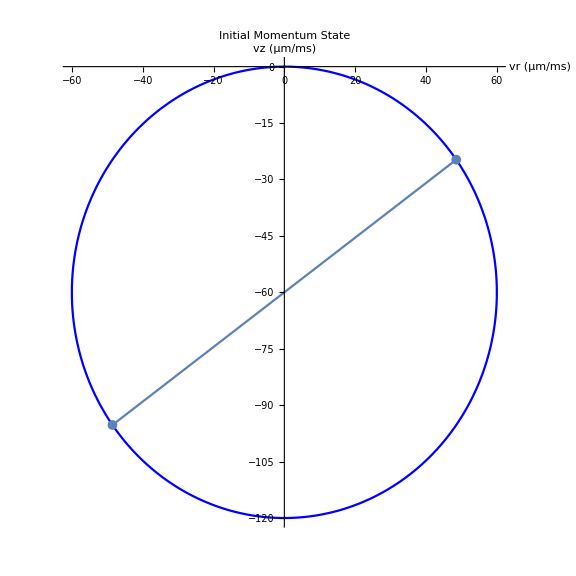

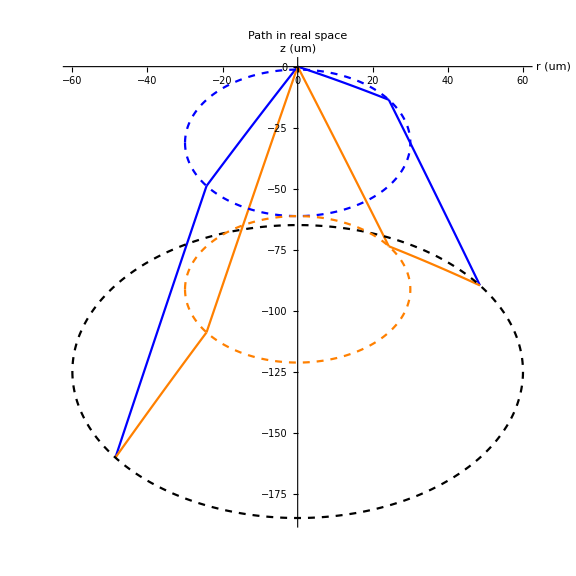

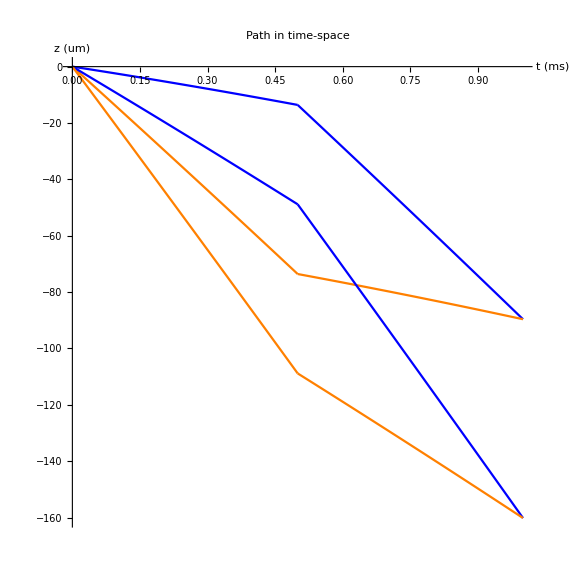

```mathematica
ϕ=Pi/5;
g0=-9.81;
u=60;(*in mm/s*)
dv=-2*u;
offset = -2*u;
tf=1;(*in milliseconds*)
vr=u*Cos[ϕ];
vz=u*Sin[ϕ]+u+offset;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
(*propogting in the positive direction*)
p1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
p2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
vr=u*Cos[ϕ+Pi];
vz=u*Sin[ϕ+Pi]+u+offset;
uh=vz+g0*tf/2+dv;
sh=s[tf/2,0,vz,g0];
vzc=vz+dv;
uhc=vzc+g0*tf/2-dv;
shc=s[tf/2,0,vzc,g0];
th=ParametricPlot[{Cos[θ]*u*tf/2, (Sin[θ]*u-u)*tf/2+1/2*g0*tf^2/4}, {θ, -Pi,Pi},PlotStyle->{Blue,Dashed}];
bh=ParametricPlot[{Cos[θ]*u*tf/2, (Sin[θ]*u-u+offset)*tf/2+1/2*g0*tf^2/4}, {θ, -Pi,Pi},PlotStyle->{Orange,Dashed}];
pc1=ParametricPlot[{{t*vr,s[t,0,vz,g0]},{t*vr,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2=ParametricPlot[{{t*vr,s[(t-tf/2),sh,uh,g0]},{t*vr,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
pc1t=ParametricPlot[{{t,s[t,0,vz,g0]},{t,s[t,0,vzc,g0]}},{t,0,tf/2},PlotStyle->{Blue,Orange}];
pc2t=ParametricPlot[{{t,s[(t-tf/2),sh,uh,g0]},{t,s[(t-tf/2),shc,uhc,g0]}},{t,tf/2,tf},PlotStyle->{Blue,Orange}];
p5=ParametricPlot[{Cos[θ]*u*tf, Sin[θ]*u*tf+g0*tf^2/2+offset*tf}, {θ, -Pi,Pi},PlotStyle->{Black,Dashed}];
p6=ParametricPlot[{Cos[θ]*u, (Sin[θ]*u+u)+offset}, {θ, -Pi,Pi},PlotStyle->{Blue}];
p7=ListPlot[{{u*Cos[ϕ+Pi],u*Sin[ϕ+Pi]+u+offset},{u*Cos[ϕ],u*Sin[ϕ]+u+offset}},PlotMarkers->{Automatic,10},Joined->True];
Show[p6,p7, ImageSize -> 72*{8, 8},AxesLabel->{"vr (μm/ms)","vz (μm/ms)"},PlotLabel ->"Initial Momentum State"]
Show[p2,p1,pc2,pc1,p5,th,bh,PlotRange->All,AxesLabel->{"r (um)","z (um)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20}, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in real space"]
Show[p2t,p1t,pc2t,pc1t,PlotRange->All,AxesLabel->{"t (ms)","z (um)"},BaseStyle -> {FontWeight -> "Bold", FontSize -> 20},PlotRange -> {{-60, 60}, {-60,60}},AspectRatio->1, ImageSize -> 72*{8, 8},AxesOrigin->{0,0},PlotLabel ->"Path in time-space"]
```

## Phase due to gravity

```mathematica
(*Validity of semi-classical approximation against vertical velocity*)
```

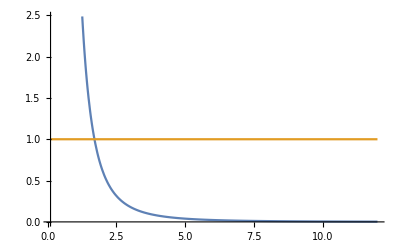

```mathematica
Plot[{V[Quantity[vz,"CentiMeters/Second"]],1},{vz,0.1,12},FrameLabel->{"vz (cm/s)","Validity"}]
```

```mathematica
(*Phase acrued before mirror pulse*)
φ1=φ[vz0,gr,t0,z0,m,vrad]
(*Phase acrued after mirror pulse*)
φ2=φ[vz0+gr*t0+Δv,gr,t0+δt,s[t0,z0,vz0,gr],m,vrad];
(*total phase acrued*)
φt=FullSimplify[φ1+φ2]
(*total phase assuming equal time between mirror and splitter*)
φT=FullSimplify[(φ1+φ2)/.δt->0];

(*Phase acrued in complementay path*)
φ1c=φ[vz0+Δv+δv,gr,t0,z0+δz,m,vrad+δvr];
(*Phase acrued after mirror pulse*)
φ2c=φ[vz0+δv+gr*t0,gr,t0+δt,s[t0,z0+δz,vz0+Δv+δv,gr],m,vrad+δvr];
(*total phase acrued*)
φtc=FullSimplify[φ1c+φ2c];
(*total phase assuming equal time between mirror and splitter*)
φTc=FullSimplify[(φ1c+φ2c)/.δt->0];

(*difference between paths*)
δφ=FullSimplify[φt-φtc]
FullSimplify[φT-φTc]
FullSimplify[(φT-φTc)/.{δv->0,δvr->0}]
FullSimplify[(φT-φTc)/.{δv->0,δvr->0,δz->0,t0->tF/2}]
(*Naive average over correlation volume*)
FullSimplify[1/(zu-zl)^2*1/(vu-vl)^2*1/(vru-vrl)^2*Integrate[Integrate[Integrate[Integrate[Integrate[Integrate[δφ,{δv,vl-vz0,vu-vz0}],{vz0,vl,vu}],{δvr,vrl-vrad,vru-vrad}],{vrad,vrl,vru}],{δz,zl-z0,zu-z0}],{z0,zl,zu}]/.δt->0]


(*Phase acrued before mirror pulse*)
φ1=φ[vz0,gr,t0,z0,m,Sqrt[vh^2-(vz0-vh)^2]];
(*Phase acrued after mirror pulse*)
φ2=φ[vz0+gr*t0+Δv,gr,t0+δt,s[t0,z0,vz0,gr],m,Sqrt[vh^2-(vz0-vh)^2]];
(*total phase acrued*)
φt=FullSimplify[φ1+φ2];
(*total phase assuming equal time between mirror and splitter*)
φT=FullSimplify[(φ1+φ2)/.δt->0];

(*Phase acrued in complementay path*)
φ1c=φ[vz0+Δv+δv,gr,t0,z0+δz,m,Sqrt[vh^2-((vz0+Δv+δv)+vh)^2]];
(*Phase acrued after mirror pulse*)
φ2c=φ[vz0+δv+gr*t0,gr,t0+δt,s[t0,z0+δz,vz0+Δv+δv,gr],m,Sqrt[vh^2-((vz0+Δv+δv)+vh)^2]];
(*total phase acrued*)
φtc=FullSimplify[φ1c+φ2c];
(*total phase assuming equal time between mirror and splitter*)
φTc=FullSimplify[(φ1c+φ2c)/.δt->0];
δφ=FullSimplify[φt-φtc];
ω=FullSimplify[1/(zu-zl)^2*1/(vu-vl)^2*Integrate[Integrate[Integrate[Integrate[δφ,{δv,vl-vz0,vu-vz0}],{vz0,vl,vu}],{δz,zl-z0,zu-z0}],{z0,zl,zu}]/.{δt->0,vh->-Δv/2}]
kern=FullSimplify[(δφ-ω)^2/.{δt->0,vh->-Δv/2}];
δω=FullSimplify[1/(zu-zl)^2*1/(vu-vl)^2*Integrate[Integrate[Integrate[Integrate[kern,{δv,vl-vz0,vu-vz0}],{vz0,vl,vu}],{δz,zl-z0,zu-z0}],{z0,zl,zu}]]
```

1/2 m t0 (vrad^2+vz0^2-2 gr z0)

1/2 m ((vrad^2+vz0^2-2 gr z0) (2 t0+δt)+2 (gr t0+vz0) (t0+δt) Δv+(t0+δt) Δv^2)

1/2 m (4 gr t0^2 Δv-δt ((δv-Δv) (2 vz0+δv+Δv)+2 vrad δvr+δvr^2-2 gr δz)-2 t0 (δv (2 vz0+δv+Δv)+δvr (2 vrad+δvr)-2 gr (δt Δv+δz)))

m t0 (-δv (2 vz0+δv+Δv)-δvr (2 vrad+δvr)+2 gr (t0 Δv+δz))

2 gr m t0 (t0 Δv+δz)

1/2 gr m tF^2 Δv

2 gr m t0^2 Δv

2 gr m t0^2 Δv

2/3 gr^2 m^2 t0^2 (zl-zu)^2

```mathematica
1/2 m ((vrad^2+vz0^2-2 gr z0) (2 t0+δt)+2 (gr t0+vz0) (t0+δt) Δv+(t0+δt) Δv^2)/.{δt->0}
```

1/2 m (2 t0 (vrad^2+vz0^2-2 gr z0)+2 t0 (gr t0+vz0) Δv+t0 Δv^2)

```mathematica
FullSimplify[1/2 m (2 t0 (vrad^2+vz0^2-2 gr z0)+2 t0 (gr t0+vz0) Δv+t0 Δv^2)]
```

1/2 m t0 (2 (vrad^2+vz0^2-2 gr z0)+2 (gr t0+vz0) Δv+Δv^2)

```mathematica
Integrate[,{δv,vl-vz0,vu-vz0}]
```

m^2 t^2 (-vl+vu) ((vl+vu-2 vz0) Δv-2 gr δz)^2

```mathematica
Solve[Cos[θ]*u0*t==Cos[γ]*u0*t+r0,θ]
```

{{θ→ConditionalExpression[-ArcCos[(r0+t u0 Cos[γ])/(t u0)]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcCos[(r0+t u0 Cos[γ])/(t u0)]+2 π C[1],C[1]∈ℤ]}}

```mathematica
Solve[(Sin[θ]*u0+u0)*t+gr*t^2/2-u0*t==(Sin[γ]*u0+u0)*t+gr*t^2/2-u0*t+z0,θ]
```

{{θ→ConditionalExpression[π-ArcSin[(z0+t u0 Sin[γ])/(t u0)]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcSin[(z0+t u0 Sin[γ])/(t u0)]+2 π C[1],C[1]∈ℤ]}}

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 3 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

StringJoin::string: String expected at position 5 in $Failed<>



<>$Failed<>
s[t_, s0_, u0_, g_] := s0 + u0*t + (1/2)*g*t^2; 

<>$Failed<>
Null

<>$Failed<>
{}



<>$Failed<>


[12.0.0.0 (6206958, 2019040601); Windows-x86-64; 3243-4626-52PU5W; paclet 12.1.148]

.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

```mathematica
φ1=φ[vz0,gr,t0,z0,m,vrad];
φ2=φ[vz0+gr*t0+Δv,gr,t0+δt,s[t,z0,vz0,gr],m,vrad]
```

1/2 m (t0+δt) (gr^2 (-1+t0^2)+vrad^2+(vz0+Δv)^2+2 gr ((-1+t0) vz0-z0+t0 Δv))

```mathematica
m (gr z0 Quantity[-1,"Seconds"]+(vrad^2+vz0^2) Quantity[1/2,"Seconds"])
```

m (gr z0 (-1 s)+(vrad^2+vz0^2) (1/2 s))

```mathematica
δφ
```

-1/2 gr^2 m (-1+t0^2) (t0+δt)+m (2 vz0+δv+Δv) (δt (vh+Δv)+t0 (2 vh+Δv))+gr m ((t0+δt) (-(-1+t0) (vz0+δv)+(1+t0) Δv)+(2 t0+δt) δz)

```mathematica
φTc
```

-1/2 m t0 (4 vh (vz0+δv+Δv)+Δv (2 (vz0+δv)+Δv)+2 gr (2 z0+t0 Δv+2 δz))

```mathematica
δφ
```

m (2 gr t0^2 Δv+δt (vh+Δv) (2 vz0+δv+Δv)+gr δt δz+t0 (2 vh (2 vz0+δv+Δv)+Δv (2 vz0+2 gr δt+δv+Δv)+2 gr δz))

```mathematica
kern
```

4 gr^2 m^2 t0^2 δz^2

```mathematica
(*Phase acrued before mirror pulse*)
φ1=φ[vz0,gr,t0,z0,m,vrad];
(*Phase acrued after mirror pulse*)
φ2=φ[vz0+gr*t0+Δv,gr,t0*2,s[t0,z0,vz0,gr],m,vrad];
φ3=φ[vz0+gr*t0*3,gr,t0,s[t0*2,s[t0,z0,vz0,gr],vz0+gr*t0+Δv,gr],m,vrad];
(*total phase acrued*)
φt=FullSimplify[φ1+φ2+φ3];
(*total phase assuming equal time between mirror and splitter*)
φT=FullSimplify[(φ1+φ2+φ3)/.δt->0]

(*Phase acrued in complementay path*)
φ1c=φ[vz0+Δv,gr,t0,z0,m,vrad];
(*Phase acrued after mirror pulse*)
φ2c=φ[vz0+gr*t0,gr,t0*2,s[t0,z0,vz0+Δv,gr],m,vrad];
φ3c=φ[vz0+gr*t0*3+Δv,gr,t0,s[t0*2,s[t0,z0,vz0+Δv,gr],vz0+gr*t0,gr],m,vrad];
(*total phase acrued*)
φtc=FullSimplify[φ1c+φ2c+φ3c];
(*total phase assuming equal time between mirror and splitter*)
φTc=FullSimplify[(φ1c+φ2c+φ3c)/.δt->0]

(*difference between paths*)
FullSimplify[(φT-φTc)/.{δv->0,δvr->0,δz->0,t0->tF/2}]
```

m t0 (2 (vrad^2+vz0^2-2 gr z0)+2 vz0 Δv+Δv^2)

m t0 (2 (vrad^2+vz0^2-2 gr z0)+2 vz0 Δv+Δv^2)

0

```mathematica
φT
```

```mathematica
(*Phase acrued before mirror pulse*)
φ1=φ[vz0,gr,t0,z0,m,vrad];
(*Phase acrued after mirror pulse*)
φ2=φ[vz0+gr*t0+Δv,gr,t0+δt,s[t0,z0,vz0,gr],m,vrad+δvr];
(*total phase acrued*)
φt=FullSimplify[φ1+φ2];
(*total phase assuming equal time between mirror and splitter*)
φT=FullSimplify[(φ1+φ2)/.δt->0];

(*Phase acrued in complementay path*)
φ1c=φ[vz0+Δv+δv,gr,t0,z0+δz,m,vrad+δvr];
(*Phase acrued after mirror pulse*)
φ2c=φ[vz0+δv+gr*t0,gr,t0+δt,s[t0,z0+δz,vz0+Δv+δv,gr],m,vrad];
(*total phase acrued*)
φtc=FullSimplify[φ1c+φ2c];
(*total phase assuming equal time between mirror and splitter*)
φTc=FullSimplify[(φ1c+φ2c)/.δt->0];
```

```mathematica
(*difference between paths*)
δφ=FullSimplify[φt-φtc]
FullSimplify[(φT-φTc)/.{δv->0,δz->0,t0->tF/2}]
```

1/2 m (4 gr t0^2 Δv-2 t0 δv (2 vz0+δv+Δv)+4 gr t0 (δt Δv+δz)+δt (-(δv-Δv) (2 vz0+δv+Δv)+2 vrad δvr+δvr^2+2 gr δz))

1/2 gr m tF^2 Δv